{{310,0.638064},{275,0.562463},{223,0.450143},{179,0.355102},{147,0.285981},{121,0.229821}}

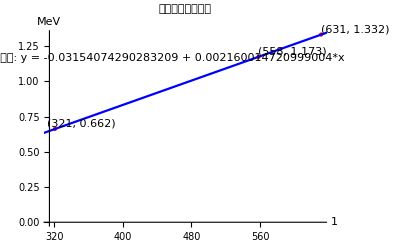

拟合方程: -0.0315407+0.00216001 x

拟合参数： | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0315407 | 0.00217351 | -14.5114 | 0.043801
x | 0.00216001 | 4.17632×10^-6 | 517.206 | 0.00123088

决定系数R.b2：0.999996

标准误差：9.16255×10^-7

```mathematica
(*定义数据点*)
data={{321,0.662},{558,1.173},{631,1.332}};

(*线性回归拟合*)
fit=LinearModelFit[data,x,x];

(*新的数据点*)
newData={310,275,223,179,147,121};

(*计算能量*)
calculatedEnergies=fit[#]&/@newData;

(*输出新数据点及其对应的能量*)
newDataWithEnergies=Transpose[{newData,calculatedEnergies}]

(*获取拟合方程*)
fitFunction=fit["BestFit"];

(*绘制数据点和拟合直线，并标出数据点的数值和拟合方程*)
Show[ListPlot[data,PlotStyle->{Red,PointSize[Large]},AxesLabel->{"1","MeV"}],Plot[fitFunction,{x,300,650},PlotStyle->Blue],PlotLabel->"数据点及拟合直线",Epilog->{Text["("<>ToString[data[[1,1]]]<>", "<>ToString[data[[1,2]]]<>")",{312,0.662},{-1,-1}],Text["("<>ToString[data[[2,1]]]<>", "<>ToString[data[[2,2]]]<>")",{558,1.173},{-1,-1}],Text["("<>ToString[data[[3,1]]]<>", "<>ToString[data[[3,2]]]<>")",{631,1.332},{-1,-1}],Text["拟合直线: y = "<>ToString[Normal[fitFunction],InputForm],{450,1.2},{0,1}]}]

(*计算误差分析*)
Print["拟合方程: ",fitFunction];
Print["拟合参数：",fit["ParameterTable"]];
Print["决定系数R.b2：",fit["RSquared"]];
Print["标准误差：",fit["EstimatedVariance"]];
```

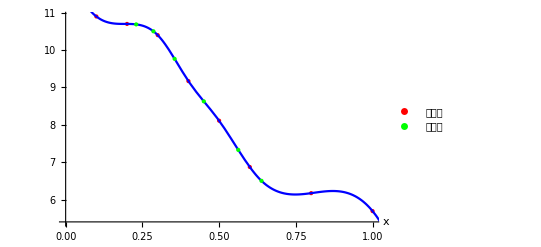
{x | 
0.638064 | 6.49977
0.562463 | 7.3281
0.450143 | 8.62785
0.355102 | 9.76456
0.285981 | 10.5031
0.229821 | 10.6876,-Graphics-}

```mathematica
(*拟合的曲线*)

(*定义数据点*)
data={{0.1,10.9},{0.2,10.7},{0.3,10.4},{0.4,9.17},{0.5,8.11},{0.6,6.87},{0.8,6.17},{1.0,5.69}};

(*样条拟合*)
splineFit=Interpolation[data,Method->"Spline"];

(*定义需要计算的点*)
points={0.6380638206068592,0.562463305371894,0.4501425398799458,0.35510189215598964,0.28598142108402147,0.2298210383380474};

(*计算这些点对应的值*)
fittedValues=splineFit/@points;

(*输出计算结果*)
fittedTable=TableForm[Transpose[{points,fittedValues}],TableHeadings->{None,{"x",""}}];

(*绘制数据点、拟合曲线及新的计算点*)
plot=Show[ListPlot[data,PlotStyle->{Red,PointSize[Large]},AxesLabel->{"x",""},PlotLegends->{"数据点"}],Plot[splineFit[x],{x,0,1.1},PlotStyle->Blue,PlotLabel->"样条拟合"],ListPlot[Transpose[{points,fittedValues}],PlotStyle->{Green,PointSize[Medium]},PlotLegends->{"计算点"}],PlotLegends->{"数据点","样条拟合","计算点"}];

(*显示结果表格和图像*)
{fittedTable,plot}
```

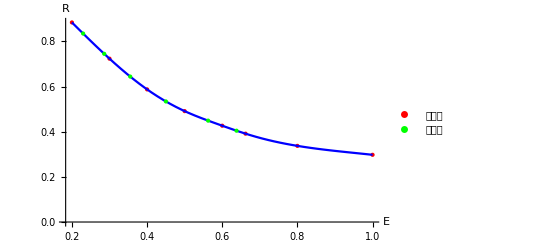
{Energy (E) | R
0.638064 | 0.404489
0.562463 | 0.449096
0.450143 | 0.534102
0.355102 | 0.644321
0.285981 | 0.745083
0.229821 | 0.83486,-Graphics-}

```mathematica
(*拟合的曲线*)

(*定义数据点*)
data={{0.2,0.8841},{0.3,0.7236},{0.4,0.5875},{0.5,0.4912},{0.6,0.4266},{0.662,0.3914},{0.8,0.3373},{1.0,0.2977}};

(*样条拟合*)
splineFit=Interpolation[data,Method->"Spline"];

(*定义需要计算的能量点*)
energyPoints={0.6380638206068592,0.562463305371894,0.4501425398799458,0.35510189215598964,0.28598142108402147,0.2298210383380474};

(*计算这些能量点对应的值*)
fittedValues=splineFit/@energyPoints;

(*输出计算结果*)
fittedTable=TableForm[Transpose[{energyPoints,fittedValues}],TableHeadings->{None,{"Energy (E)","R"}}];

(*绘制数据点和样条拟合曲线及计算点*)
plot=Show[ListPlot[data,PlotStyle->{Red,PointSize[Large]},AxesLabel->{"E","R"},PlotLegends->{"数据点"}],Plot[splineFit[x],{x,0.2,1.0},PlotStyle->Blue,PlotLabel->"样条拟合",AxesLabel->{"E","R"}],ListPlot[Transpose[{energyPoints,fittedValues}],PlotStyle->{Green,PointSize[Medium]},PlotLegends->{"计算点"}],PlotLegends->{"数据点","样条拟合","计算点"}];

(*显示结果表格和图像*)
{fittedTable,plot}
```

```mathematica
(*定义数组*)
N1={12148,10334,8096,7488,6416,7982};
R={0.40448890651960123,0.4490962620538123,0.5341021068829621,0.6443213225242196,0.7450830049591655,0.83485976288315};
eta={6.499772114618485,7.328101703602218,8.627846621099549,9.76455793754295,10.503066483228785,10.687640690255227};

(*计算公式结果*)
results=N1/(R*eta);

(*以第一个数据为基准（分母）进行计算*)
normalizedResults=results/results[[1]];

(*输出计算结果*)
TableForm[Transpose[{N1,R,eta,results,normalizedResults}],TableHeadings->{None,{"N1","R","eta","Result","Normalized Result"}}]
```

N1 | R | eta | Result | Normalized Result
12148 | 0.404489 | 6.49977 | 4620.62 | 1.
10334 | 0.449096 | 7.3281 | 3140.06 | 0.679575
8096 | 0.534102 | 8.62785 | 1756.89 | 0.380228
7488 | 0.644321 | 9.76456 | 1190.17 | 0.257579
6416 | 0.745083 | 10.5031 | 819.867 | 0.177437
7982 | 0.83486 | 10.6876 | 894.574 | 0.193605

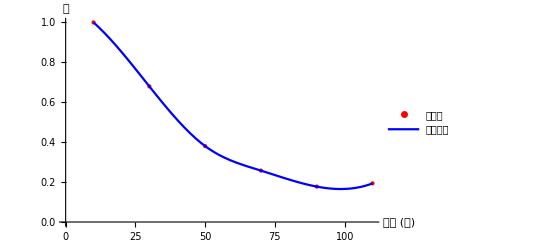

```mathematica
(*定义角度和对应的数据点*)angles={10,30,50,70,90,110};
values=normalizedResults;

(*样条拟合*)
splineFit=Interpolation[Transpose[{angles,values}],Method->"Spline"];

(*绘制数据点和拟合曲线*)
plot=Show[ListPlot[Transpose[{angles,values}],PlotStyle->{Red,PointSize[Large]},AxesLabel->{"角度 (度)","值"},PlotLegends->{"数据点"}],Plot[splineFit[x],{x,10,110},PlotStyle->Blue,PlotLabel->"样条拟合曲线",PlotLegends->{"拟合曲线"}]];

(*显示图像*)
plot
```

```mathematica
(*定义角度θ，单位为度*)
theta={0,10,20,30,40,50,60,70,80,90,100,110,120};

(*将角度转换为弧度*)
thetaRad=theta*(Pi/180);

(*计算 1-cos(θ)*)
oneMinusCosTheta=N[1-Cos[thetaRad]];

(*计算 hν'*)
hνPrime=0.662/(1+(0.662/0.511)*oneMinusCosTheta);

(*计算 a*)
a=((2.818*10^-3)^2/2)*(hνPrime/0.662)^2*(0.662/hνPrime+hνPrime/0.662-Sin[thetaRad]^2);

(*第一个数为分母，计算 a/7.94112*10^-6*)
normalizedA=a/a[[2]];

(*输出结果表格*)
TableForm[Transpose[{theta,oneMinusCosTheta,hνPrime,a,normalizedA}],TableHeadings->{None,{"θ (度)","1 - Cos(θ)","hν'","a","a / (7.523829687777629*10^-6)"}}]
```

θ (度) | 1 - Cos(θ) | hν' | a | a / (7.523829687777629*10^-6)
0 | 0. | 0.662 | 7.94112×10^-6 | 1.05546
10 | 0.0151922 | 0.649222 | 7.52383×10^-6 | 1.
20 | 0.0603074 | 0.614027 | 6.45165×10^-6 | 0.857495
30 | 0.133975 | 0.564094 | 5.11918×10^-6 | 0.680396
40 | 0.233956 | 0.508024 | 3.87534×10^-6 | 0.515076
50 | 0.357212 | 0.452567 | 2.89407×10^-6 | 0.384653
60 | 0.5 | 0.40176 | 2.2004×10^-6 | 0.292457
70 | 0.65798 | 0.357372 | 1.74635×10^-6 | 0.232109
80 | 0.826352 | 0.319724 | 1.46672×10^-6 | 0.194943
90 | 1. | 0.28839 | 1.30445×10^-6 | 0.173376
100 | 1.17365 | 0.26265 | 1.21714×10^-6 | 0.161771
110 | 1.34202 | 0.241731 | 1.17569×10^-6 | 0.156262
120 | 1.5 | 0.224922 | 1.16101×10^-6 | 0.154311

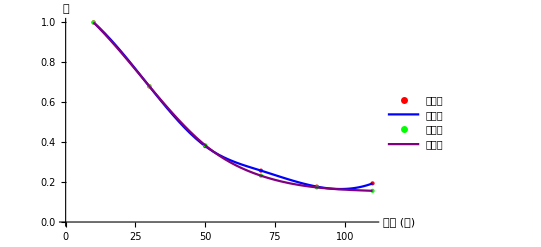

```mathematica
(*定义角度和对应的两个数据集*)angles={10,30,50,70,90,110};
values1=normalizedResults;

(*样条拟合*)
splineFit1=Interpolation[Transpose[{angles,values1}],Method->"Spline"];
splineFit2=Interpolation[Transpose[{angles,values2}],Method->"Spline"];

(*绘制数据点和拟合曲线*)
plot=Show[ListPlot[Transpose[{angles,values1}],PlotStyle->{Red,PointSize[Large]},AxesLabel->{"角度 (度)","值"},PlotLegends->{"实验值"}],Plot[splineFit1[x],{x,10,110},PlotStyle->Blue,PlotLabel->"实验值拟合曲线",PlotLegends->{"实验值"}],ListPlot[Transpose[{angles,values2}],PlotStyle->{Green,PointSize[Large]},PlotLegends->{"理论值"}],Plot[splineFit2[x],{x,10,110},PlotStyle->Purple,PlotLabel->"理论值拟合曲线",PlotLegends->{"理论值"}]];

(*显示图像*)
plot
```